Размер остовного дерева: 179

Остовное дерево:

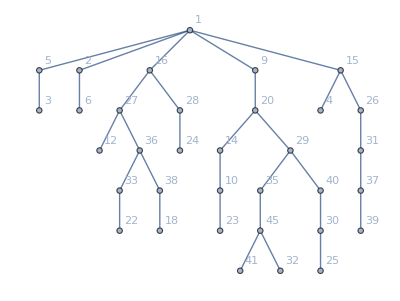

Остовное дерево на исходном графе:

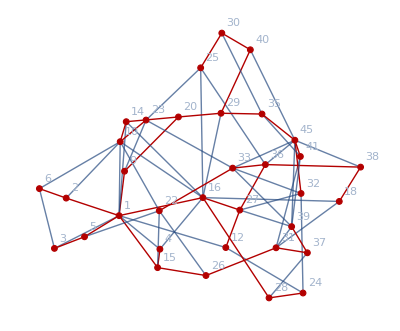

```mathematica
(*Раскраска графа*)
Unprotect[E];

E={{1,2,5},{1,3,11},{1,4,11},{1,5,4},{1,9,5},{1,10,11},{1,12,10},{1,14,12},{1,15,6},{1,16,6},{2,6,4},{2,10,11},{3,5,4},{3,6,11},{4,15,5},{4,16,7},{5,22,10},{6,10,10},{9,20,7},{9,23,10},{10,14,4},{10,16,11},{10,22,9},{10,23,4},{12,24,10},{12,27,5},{14,16,12},{14,20,6},{15,22,9},{15,26,5},{16,18,10},{16,25,11},{16,27,4},{16,28,9},{16,29,7},{18,31,10},{18,38,6},{20,29,4},{22,26,10},{22,33,8},{23,25,8},{23,33,9},{24,28,6},{24,32,9},{25,30,5},{25,36,12},{26,31,6},{27,32,9},{27,36,6},{27,39,6},{28,37,12},{29,35,4},{29,40,7},{30,35,11},{30,40,6},{31,37,5},{31,39,6},{31,41,8},{32,33,9},{32,45,6},{33,36,5},{33,39,10},{33,45,10},{35,41,6},{35,45,5},{36,38,9},{36,45,10},{37,39,4},{38,45,11},{39,41,12},{39,45,10},{40,45,12},{41,45,4}};

(*Edge lists*)
edgeList=Map[Function[x,UndirectedEdge[Part[x,1],Part[x,2]]],E];
weights=Map[Function[x,Part[x,3]],E];
graph=Graph[edgeList,EdgeWeight->weights];

graph=SetProperty[graph,VertexLabels->"Name"];
graph=SetProperty[graph,GraphLayout->{VertexLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}}];
graph;
vertexCount=VertexCount[graph];

sortedE=SortBy[E,Last];

FindSet[vertices_List,vertex_]:=Module[{i},
For[i=1,i≤Length[vertices],i++,
If[MemberQ[vertices⟦i⟧,vertex],Return[i];];
];
Return[0];
]

vertices={};
edges={};
edgePaths={};
AppendTo[vertices,{sortedE⟦1⟧⟦1⟧,sortedE⟦1⟧⟦2⟧}];
AppendTo[edges,UndirectedEdge[sortedE⟦1⟧⟦1⟧,sortedE⟦1⟧⟦2⟧]];
insCount=2;
treeSize=sortedE⟦1⟧⟦3⟧;

For[i=2,i≤Length[sortedE],i++,
If[insCount≥vertexCount&&Length[vertices]==1,Break[]];
v1=sortedE⟦i⟧⟦1⟧;
v2=sortedE⟦i⟧⟦2⟧;
set1=FindSet[vertices,v1];
set2=FindSet[vertices,v2];
If[set1==set2≠0,Continue[]];
(*append edge in all other cases*)
AppendTo[edges,UndirectedEdge[sortedE⟦i⟧⟦1⟧,sortedE⟦i⟧⟦2⟧]];
treeSize=treeSize+sortedE⟦i⟧⟦3⟧;
(*new set*)
If[set1==set2==0,AppendTo[vertices,{sortedE⟦i⟧⟦1⟧,sortedE⟦i⟧⟦2⟧}];
insCount=insCount+2;
Continue[];];
If[set1≠set2&&set1>0&&set2>0,
(*join sets*)
uSet=Join[vertices⟦set1⟧,vertices⟦set2⟧];
delList=Sort[{{set1},{set2}}];
vertices=Delete[vertices,delList⟦2⟧];
vertices=Delete[vertices,delList⟦1⟧];
AppendTo[vertices,uSet];
Continue[];
]
(*set1≠set2 && set1==0 || set2==0*)
AppendTo[vertices⟦set1+set2⟧,sortedE⟦i⟧⟦1⟧*Boole[set1==0]+sortedE⟦i⟧⟦2⟧*Boole[set2==0]];
insCount++;
];

Print["Размер остовного дерева: ",treeSize];
Print["Остовное дерево:"];
treeGraph=Graph[edges,VertexLabels->"Name"]
Print["Остовное дерево на исходном графе:"];
highlightedGraph=HighlightGraph[graph,treeGraph]
```